# A Story in “His-Story”

Henry Hyunsuk Kim

### Introduction

Growing up with a perennial sense of anomie and alienation as I belonged neither here nor there, I was often told how "The War" destroyed our homeland. Missionaries to Korea, The War, and then structure, agency, and contingency. I still laugh regarding the ironic consequences of the U.S.' 1965 Immigration Reform Act.

As I curiously followed one academic trajectory after another, I realized that computational thinking may assist traditional historiography. Poor social exegesis feeds into biblical exegesis, resulting in iatrogenesis and eisegesis. Or, as the only sign that has hung on my office door for over a decade states: “Sociology without theology is powerless and theology without sociology is blind.” I am beginning to wonder how Mathematica may help bridge these disciplines.

### Grunt Work - Entering the Data

Have you ever read microfilm and tried to enter seemingly illegible data into Excel?

### Grunt Work for Nothing?

After entering all of the data into Excel, and spending countless hours learning NodeXL, was it for nothing? I got some nice pictures and it spat out the "standard" SNA metrics, but I felt limited in analyzing the data with the pre-set GUI functions.

### Hope?

Charles Pooh visited our campus in 2013 (brokered by Hank Allen).

### The Fire Almost dies and is Rekindled

Charles left. And after looking at a blank screen and blinking cursor ...  again ... I remembered the joys of importing my first set of data from Excel into Mathematica (2016) to try to create sociograms.

### Using Iconize for my Data Variable

```mathematica
underwood=;
Dimensions@%
```

{317,7}

### Trying Again...

Stephen Wolfram visited our campus (2017, brokered by Hank Allen) and gave out free copies of his EIWL (2nd Ed.)  Hannah Garringer (one of my RAs) and I began to read this text. I told her I had already read the 1st Ed. many times - to no avail. Hannah encouraged me to attend a conferences as well as the 2019 Summer Program.

### A Story Continues

### These are the Data Columns:

```mathematica
First@underwood
```

{From,To,Year,Month,Date,Location,Content}

### How many letters were sent? How many unique senders?

```mathematica
senders=First/@Rest@underwood;
"letters sent"->Length@senders
"unique senders"->Length@DeleteDuplicates@senders
```

letters sent→316

unique senders→19

```mathematica
tallySenders=Tally[senders]
```

{{H.G. Underwood,254},{Lillias Horton,14},{H.G. Underwood, Daniel L. Gifford, S. Moffet,1},{H.G. Underwood, D.L. Gifford,1},{Rev. W.H. Roberts,1},10,{Dr. Goucher,1},{Thomas Sammons,1},{John F. Genso,2},{E.H. Miller and H.G. Underwood,1}}
 |  |  |  |

### A PieChart was made from the button “tally barchart” from the suggestion bar:

```mathematica
Show[Import["C:\\Users\\hekim\\Documents\\WSS-Template\\tally barchart.PNG"],ImageSize->Medium]
```

-Graphics-

```mathematica
PieChart[Apply[Labeled,Reverse[tallySenders,2],{1}]]
```

-Graphics-

### A BarChart was also made:

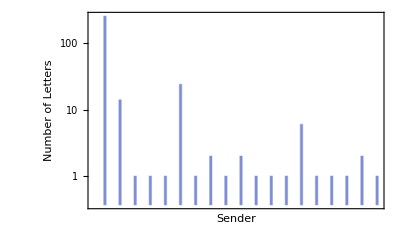

```mathematica
BarChart[tallySenders,Axes->False,Frame->True,FrameLabel->{"Sender","Number of Letters"}, ScalingFunctions->"Log"]
```

### How many letters were received? How many unique receivers?

```mathematica
recipients=underwood[[2;;,2]];
"letters received"->Length@recipients
"unique recipients"->Length@DeleteDuplicates@recipients
```

letters received→316

unique recipients→32

```mathematica
tallyRecipients = Tally[recipients]
```

{{F.F. Ellinwood,136},{Board of Foreign Missions of the Presbyterian Church of America,3},{Allen,2},{Dr. Wells,1},{Mrs. Hepburn,1},{H.G. Underwood,11},21,{Underwood's Father and Mother,4},{Mr. Sharp,1},{Field Board of Managers,1},{Dr. Speer,3},{Dr. North,1}}
 |  |  |  |

### Using the suggestion bar to make another PieChart:

```mathematica
PieChart[Apply[Labeled,Reverse[tallyRecipients,2],{1}]]
```

-Graphics-

### And a respective BarChart:

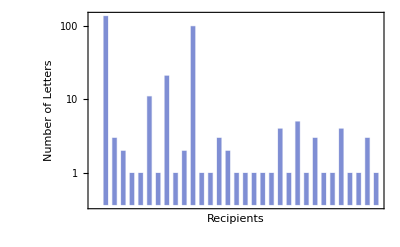

```mathematica
BarChart[tallyRecipients,Axes->False,Frame->True,FrameLabel->{"Recipients","Number of Letters"}, ScalingFunctions->"Log"]
```

### Is a picture really worth a thousand words?

This graph visualizes the directed network with the vertices labeled as a respective sender or recipient:

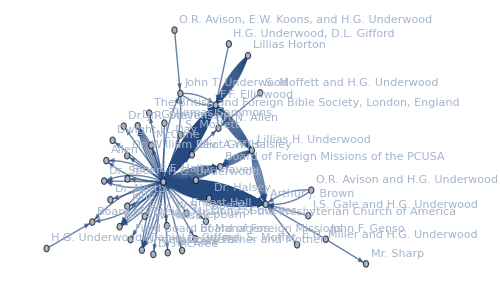

```mathematica
correspondenceNetwork=Graph[Thread[underwood[[2;;,1]]->underwood[[2;;, 2]]], VertexLabels -> "Name",ImageSize -> 500]
```

This is the same graph with the vertex names replaced with a ClosenessCentrality measure:

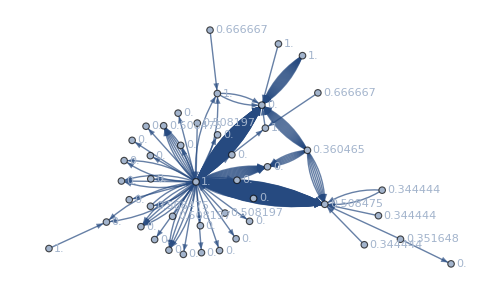

```mathematica
Graph[correspondenceNetwork,VertexLabels -> "ClosenessCentrality"]
```

### Proof of Concept?

I chose to use ClosenessCentrality as an example of a social network analysis (SNA) metric. Though it may not have been the best metric, this substantiates a proof of concept - other metrics may be employed. Below the highest twenty scores were extracted based on this measure:

```mathematica
Thread[{VertexList[correspondenceNetwork], ClosenessCentrality[correspondenceNetwork]}]//SortBy[#,Last]&//Reverse//Dataset
```

Dataset[<>]

### Time Series?

An interesting exploration regarding SNA research entails creating a time series. As I began to research with respect to SNA and possible aspects of complexity, I began to wonder if it was possible to analyze a "growth" of the network. This particular network spans from 1886 to 1915. I ascertained the smallest and greatest values from the data set, starting with the second row (precluding the headings) of the third column (the column with the years).

```mathematica
underwood[[2;;,3]]//MinMax
```

{1866.,1915.}

### A Histogram concerning letters sent (or received) by year

It is possible that Underwood’s network increased their communications in conjunction with the Japanese annexation of Korea in 1910.

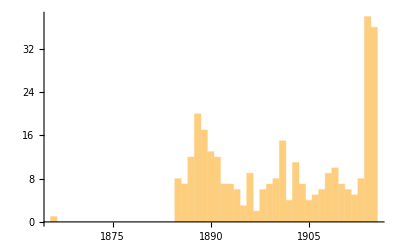

```mathematica
Histogram[underwood[[2;;,3]],{1}]
```

### From a Chaotic Region to a Basin of Attraction

Upon my arrival to the Wolfram Summer School (2019), I once again felt a sense of anomie and alienation. And after a few days... of landing a mentor ... thank you for your  kindness and help Bob Nachbar (!) as I tried to extract particular years.

### Before

Below is one year that was selected:

```mathematica
Cases[underwood,{__,1866.,_,_,_,_}]//Length
```

1

### After

Below is a range of dates that was selected from 1866 to 1900:

```mathematica
Cases[underwood,{__,year_/;1866.≤year≤1900.,_,_,_,_}]//Length
```

145

### My story continues in His-story...

I have PILES of "historical" data in Excel. This paper in some ways represents a punctiliar moment. Honestly, this assignment was not easy and there is so much I need to (re-)learn. And, I need to learn how to clean and present the data  better, choose better SNA metrics, and perhaps create a Delayed function for the analyses and Manipulate function for visualizations. However, I am grateful for the learning experiences I have had thus far.  And I am still having a lot of fun learning and exploring.